## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= D[p[t, xt, yt], t]==λt*D[yt*p[t, xt, yt], xt]+D[yt*p[t, xt, yt], yt]-D[xt*p[t, xt, yt],yt]+(αt^2/2)D[p[t, xt, yt],{xt,2}]+(αt^2/2)D[p[t, xt, yt],{yt,2}]
```

p^(1,0,0)[t,xt,yt]==p[t,xt,yt]-xt p^(0,0,1)[t,xt,yt]+yt p^(0,0,1)[t,xt,yt]+1/2 αt^2 p^(0,0,2)[t,xt,yt]+yt λt p^(0,1,0)[t,xt,yt]+1/2 αt^2 p^(0,2,0)[t,xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{αt,0},{0,αt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{αt,0},{0,αt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{αt^2/2+αt^2/(2 λt)+(αt^2 λt)/2,αt^2/(2 λt)},{αt^2/(2 λt),αt^2/2+αt^2/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.05, 0.1, 0.2, 0.4, 0.5};
αts = {1.0};
tfs = 5/λts;
params = Flatten[Table[{λt->l, αt->a}, {l, λts}, {a, αts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αt="<>ToString[k], {l, λts},{a, αts}], 1];
```

{{λt→0.05,αt→1.},{λt→0.1,αt→1.},{λt→0.2,αt→1.},{λt→0.4,αt→1.},{λt→0.5,αt→1.}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
```

{3.24423,2.35584,1.76068,1.39642,1.32288}

{3.24037,2.34521,1.73205,1.32288,1.22474}

```mathematica
deltaWidth = 0.2;
deltaVar = deltaWidth^2
minCell = deltaWidth/2
```

0.04

0.1

```mathematica
Sqrt[αts[[1]]^2/2]
```

0.707107

#### Boundary condition at x~* =1. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 5
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=-5*xtStds
ytrs = xt0+5*ytStds
```

5

{-16.2211,-11.7792,-8.80341,-6.98212,-6.61438}

{21.2211,16.7792,13.8034,11.9821,11.6144}

{-16.2211,-11.7792,-8.80341,-6.98212,-6.61438}

{21.2019,16.726,13.6603,11.6144,11.1237}

{{0.04,0},{0,0.04}}

{{0.2,0},{0,0.2}}

{ImplicitRegion[-16.2211≤xt≤21.2211&&-16.2211≤yt≤21.2019,{xt,yt}],ImplicitRegion[-11.7792≤xt≤16.7792&&-11.7792≤yt≤16.726,{xt,yt}],ImplicitRegion[-8.80341≤xt≤13.8034&&-8.80341≤yt≤13.6603,{xt,yt}],ImplicitRegion[-6.98212≤xt≤11.9821&&-6.98212≤yt≤11.6144,{xt,yt}],ImplicitRegion[-6.61438≤xt≤11.6144&&-6.61438≤yt≤11.1237,{xt,yt}]}

{ElementMesh[{{-16.2211,21.2211},{-16.2211,21.2019}},{TriangleElement[<22140>]}],ElementMesh[{{-11.7792,16.7792},{-11.7792,16.726}},{TriangleElement[<12802>]}],ElementMesh[{{-8.80341,13.8034},{-8.80341,13.6603}},{TriangleElement[<8084>]}],ElementMesh[{{-6.98212,11.9821},{-6.98212,11.6144}},{TriangleElement[<5564>]}],ElementMesh[{{-6.61438,11.6144},{-6.61438,11.1237}},{TriangleElement[<5110>]}]}

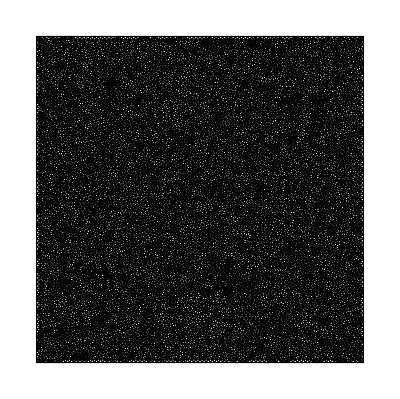

```mathematica
icPos =Table[{xt0, xt0}, 5];
icVar ={{deltaVar, 0},{0, deltaVar}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
Sqrt[icVar]
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  p[t, xtl, yt]==0,
           p[t, xtr, yt]==0,
           p[t, xt, ytr]==0,
           p[t, xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}]
meshes = Table[ToElementMesh[o, MaxCellMeasure->minCell], {o, Ω}]
meshes[[1]]["Wireframe"]
```

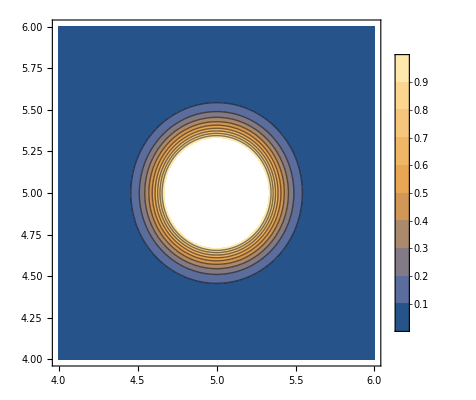

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xt0-1, xt0+1}, {yt, xt0-1, xt0+1}, PlotRange->{0,1}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, tf_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[0, xt,yt]== ic}, bc],
                                   p,{t, 0, tf},{xt, yt}∈reg, 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[(p/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes, tfs}];
```

```mathematica
Manipulate[Plot3D[solsIc0[[1]][t, xt, yt], {xt, xtls[[1]],xtrs[[1]]}, {yt, ytls[[1]],ytrs[[1]]}, AxesLabel->{xt, yt}, PlotRange->{-0.01, 0.3}, PlotLegends->Automatic],{t, 0, 100}]
```

```mathematica
Manipulate[ContourPlot[solsIc0[[1]][t, xt, yt],{xt, xtls[[1]],xtrs[[1]]}, {yt, ytls[[1]],ytrs[[1]]}, AxesLabel->{xt, yt},PlotRange->{-0.001, 1}, ColorFunction->ColorData[{"CherryTones",{-0.001,1}}],ColorFunctionScaling->False, PlotLegends->Automatic], {t, 0, 10}]
```